This script is a part of ANGEL project.
V 1.0.0
2017.12.14
(C) Vulpes Corsac

```mathematica
Clear["Global`*"];
```

```mathematica
λ=1940;
importDir="ImportData";
exportDir="ExportData";
```

```mathematica
BeamPropogationFunction[A2_,A1_,A0_,x_]:=Re[√(A2 x^2+A1 x+A0)];(* Hyperbolic fitting function for beam parameters calculation *)
```

```mathematica
data=N[{
{250-220+44.7+0.7,(1880+1950)/2},
{250-222+44.7+0.7,(1750+1850)/2},
{250-224+44.7+0.7,(1630+1700)/2},
{250-226+44.7+0.7,(1480+1540)/2},
{250-230+44.7+0.7,(1240+1270)/2},
{250-235+44.7+0.7,(920+950)/2},
{250-236+44.7+0.7,(860+890)/2},
{250-237+44.7+0.7,(800+830)/2},
{250-238+44.7+0.7,(730+760)/2},
{250-239+44.7+0.7,(670+700)/2},
{250-240+44.7+0.7,(600+630)/2},
{250-241+44.7+0.7,(540+550)/2},
{250-242+44.7+0.7,(480+490)/2},
{250-243+44.7+0.7,(420+430)/2},
{250-244+44.7+0.7,(350+360)/2},
{250-245+44.7+0.7,(290+300)/2},
{250-246+44.7+0.7,230/1},
{250-247+44.7+0.7,170/1},
{250-248+44.7+0.7,130/1},
{250-249+44.7+0.7,100/1},
{12.25+0.7,(2270+2310)/2},
{15.8+0.7,(2020+2080)/2},
{21.1+0.7,(1620+1700)/2},
{29.1+0.7,(1050+1100)/2},
{30.8+0.7,(950+990)/2},
{34.1+0.7,(730+760)/2},
{38.6+0.7,(440+450)/2}
}];
```

```mathematica
nlm=NonlinearModelFit[data,BeamPropogationFunction[A2,A1,A0,x],{A2,A1,A0},x];
parametersTable = nlm["ParameterTable"];
A2fit=parametersTable[[1,1,2,2]];
δA2fit=parametersTable[[1,1,2,3]];
A1fit=parametersTable[[1,1,3,2]];
δA1fit=parametersTable[[1,1,3,3]];
A0fit=parametersTable[[1,1,4,2]];δA0fit=parametersTable[[1,1,4,3]];
```

```mathematica
z0=Re[-A1fit/(2A2fit)];
δz0=Re[((2A2fit) (-δA1fit)+(-A1fit)(2δA2fit))/(2A2fit)^2];
dσ0=Re[1/(2 √A2fit)√(4A0fit A2fit-A1fit^2)];δdσ0=Re[1/(2 √A2fit)^2((2 √A2fit) ((4(A0fit δA2fit+A2fit δA0fit)+2 A1fit δA1fit)/(2 √(4A0fit A2fit-A1fit^2)))+(√(4A0fit A2fit-A1fit^2))(1/2 δA2fit/(2 A2fit)))];
Θσ=Re[√A2fit];
δΘσ=Re[δA2fit/(2 A2fit)];
zR=Re[1/(2A2fit)√(4A0fit A2fit-A1fit^2)];
δzR=Re[1/(2A2fit)^2((2A2fit) ((4(A0fit δA2fit+A2fit δA0fit)+2 A1fit δA1fit)/(2 √(4A0fit A2fit-A1fit^2)))+(√(4A0fit A2fit-A1fit^2))(2δA2fit))];
M2=Re[π/(8λ)√(4A0fit A2fit-A1fit^2)];δM2=Re[π/(8λ)(4(A0fit δA2fit+A2fit δA0fit)+2 A1fit δA1fit)/(2 √(4A0fit A2fit-A1fit^2))];
```

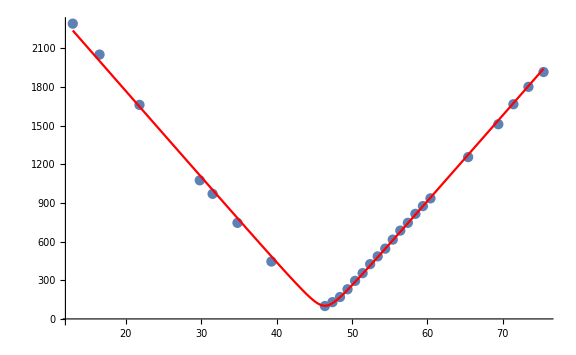

-Graphics-

```mathematica
min=Min[data[[All,1]]];
max=Max[data[[All,1]]];
Show[
ListPlot[data,ColorFunction->Function[{x,y},Blue],ImageSize->Large,PlotRange->All],
Plot[BeamPropogationFunction[A2fit,A1fit,A0fit,x],{x,min,max},ColorFunction->Function[{x,y},Red],ImageSize->Large,PlotRange->All]
]
```

```mathematica
FindMinimum[BeamPropogationFunction[A2fit,A1fit,A0fit,x],x]
```

{102.158,{x→46.3995}}

```mathematica
(* θ=4/π λ/(2 ω9) *) 
θ1=ArcTan[(1915-230)/(75400-49400)];
θ2=ArcTan[(2290-445)/(39300-12900)];
{ω1=4./π (λ×10^-3)/(2 θ1),
ω2=4./π (λ×10^-3)/(2 θ2)}
```

{19.0837,17.7009}

```mathematica
Sort[data]//TableForm
```

12.95 | 2290.
16.5 | 2050.
21.8 | 1660.
29.8 | 1075.
31.5 | 970.
34.8 | 745.
39.3 | 445.
46.4 | 100.
47.4 | 130.
48.4 | 170.
49.4 | 230.
50.4 | 295.
51.4 | 355.
52.4 | 425.
53.4 | 485.
54.4 | 545.
55.4 | 615.
56.4 | 685.
57.4 | 745.
58.4 | 815.
59.4 | 875.
60.4 | 935.
65.4 | 1255.
69.4 | 1510.
71.4 | 1665.
73.4 | 1800.
75.4 | 1915.

```mathematica
Export[NotebookDirectory[]<>"Beam.xlsx",Sort[data]];
```

```mathematica
sol1=FindFit[{{49.4,230},{75.4,1915}},k x + b,{k, b},x]
sol2=FindFit[{{12.9,2290},{39.3,445}},k x + b,{k, b},x]
k1=k/.sol1;
b1=b/.sol1;
k2=k/.sol2;
b2=b/.sol2;
Solve[k1 x+b1==k2 x+b2,x][[1]]
```

{k→64.8077,b→-2971.5}

{k→-69.8864,b→3191.53}

{x→45.7558}